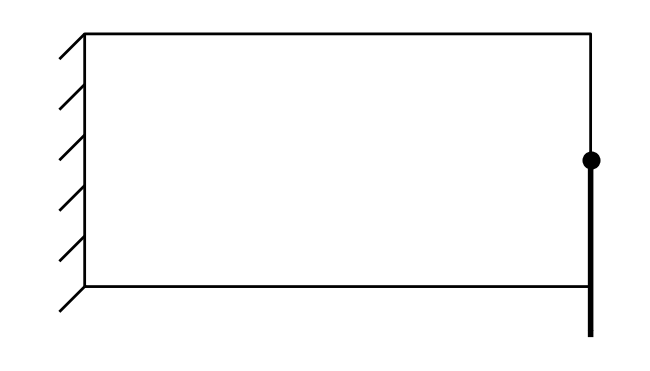

```mathematica
Graphics[
{
AbsoluteThickness[2],
Line[{{0,0},{0,1},{2,1},{2,0},{0,0}}],
PointSize[0.02],
Point[{2,0.5}],
Line[{{0,#},{-0.1,#-0.1}}]&/@Range[0,1,0.2],
AbsoluteThickness[4],
Arrowheads[0.06],
Arrow[{{2,0.5},{2,-0.2}}]
}
]
```

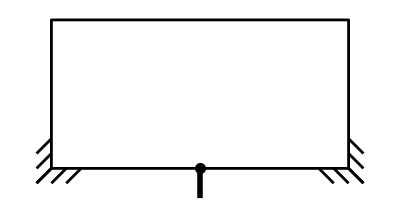

```mathematica
Graphics[
{
AbsoluteThickness[2],
Line[{{0,0},{0,1},{2,1},{2,0},{0,0}}],
PointSize[0.02],
Point[{1,0}],
Line[{{0,#},{-0.1,#-0.1}}]&/@Range[0,0.2,0.1],
Line[{{#,0},{#-0.1,-0.1}}]&/@Range[0,0.2,0.1],
Line[{{2,#},{2.1,#-0.1}}]&/@Range[0,0.2,0.1],
Line[{{#,0},{#+0.1,-0.1}}]&/@Range[2,1.8,-0.1],
AbsoluteThickness[4],
Arrowheads[0.06],
Arrow[{{1,0},{1,-0.2}}]
}
]
```